## Problem 1

### S=2

```mathematica
ρ[w_]:=w^2-w
σ[w_]:=3 w/2-1/2
z[θ_]:=ρ[Exp[I θ]]/σ[Exp[I θ]]
```

```mathematica
(*Determine the order of the method*)
Series[ρ[Exp[w]]-w σ[Exp[w]],{w,0,5}]
```

(5 w^3)/12+(3 w^4)/8+(47 w^5)/240+O[w]^6

```mathematica
(*Determine its region of stability*)
```

```mathematica
p[w_,k_]:=ρ[w]-k σ[w]
Solve[p[w,k]==0,w]
```

{{w→1/4 (2+3 k-√(4+4 k+9 k^2))},{w→1/4 (2+3 k+√(4+4 k+9 k^2))}}

```mathematica
root[k_]:=Max[Abs[1/4 (2+3 k-√(4+4 k+9 k^2))],Abs[1/4 (2+3 k+√(4+4 k+9 k^2))]]
```

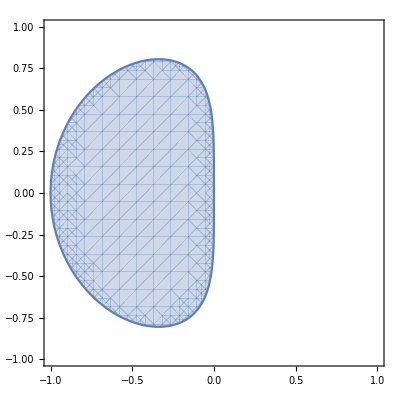

```mathematica
RegionPlot[root[x+I y]≤1,{x,-1,1},{y,-1,1}]
```

### S=3

```mathematica
ρ[w_]:=w^3-w^2
σ[w_]:=23 w^2/12-4 w/3+5/12
z[θ_]:=ρ[Exp[I θ]]/σ[Exp[I θ]]
```

```mathematica
(*Determine the order of the method*)
Series[ρ[Exp[w]]-w σ[Exp[w]],{w,0,5}]
```

(3 w^4)/8+(193 w^5)/360+O[w]^6

```mathematica
(*Determine its region of stability*)
```

```mathematica
p[w_,k_]:=ρ[w]-k σ[w];
roots[k_]:=w/.Solve[p[w,k]==0,w]
```

```mathematica
root[k_]:=Max[Abs[roots[k]]]
```

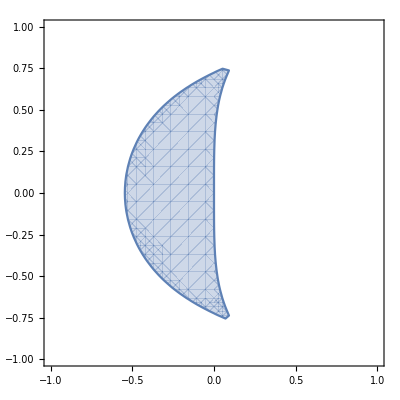

```mathematica
RegionPlot[root[x+I y]≤1,{x,-1,1},{y,-1,1}]
```

### Adams-Moulton

```mathematica
ρ[w_]:=w^2-w
σ[w_]:=5 w^2/12+2 w/3-1/12
z[θ_]:=ρ[Exp[I θ]]/σ[Exp[I θ]]
```

```mathematica
(*Determine the order of the method*)
Series[ρ[Exp[w]]-w σ[Exp[w]],{w,0,5}]
```

-w^4/24-(17 w^5)/360+O[w]^6

```mathematica
(*Determine its region of stability*)
```

```mathematica
p[w_,k_]:=ρ[w]-k σ[w];
roots[k_]:=w/.Solve[p[w,k]==0,w]
```

```mathematica
root[k_]:=Max[Abs[roots[k]]]
```

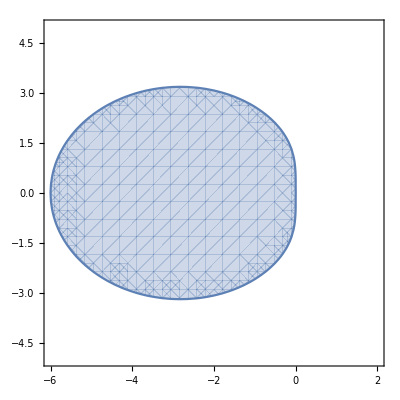

```mathematica
RegionPlot[root[x+I y]≤1,{x,-6,2},{y,-5,5}]
```

## Problem 2

### S=2

```mathematica
ρ[w_]:=w^2-4 w/3+1/3
σ[w_]:=2 w^2/3
z[θ_]:=ρ[Exp[I θ]]/σ[Exp[I θ]]
```

```mathematica
(*Determine the order of the method*)
Series[ρ[Exp[w]]-w σ[Exp[w]],{w,0,5}]
```

-(2 w^3)/9-(5 w^4)/18-(17 w^5)/90+O[w]^6

```mathematica
(*Determine its region of stability*)
```

```mathematica
p[w_,k_]:=ρ[w]-k σ[w]
Solve[p[w,k]==0,w]
```

{{w→(-2-√(1+2 k))/(-3+2 k)},{w→(-2+√(1+2 k))/(-3+2 k)}}

```mathematica
p[w_,k_]:=ρ[w]-k σ[w];
roots[k_]:=w/.Solve[p[w,k]==0,w]
root[k_]:=Max[Abs[roots[k]]]
```

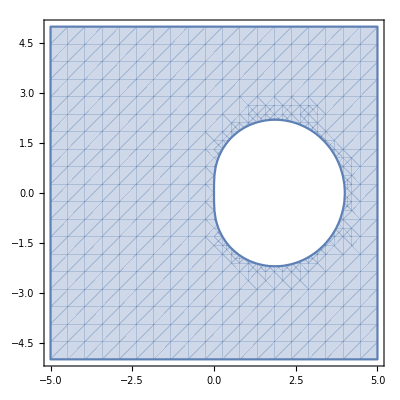

```mathematica
RegionPlot[root[x+I y]≤1,{x,-5,5},{y,-5,5}]
```

### S=3

```mathematica
ρ[w_]:=w^3-18 w^2/11+9 w/11-2/11
σ[w_]:=6 w^3/11
z[θ_]:=ρ[Exp[I θ]]/σ[Exp[I θ]]
```

```mathematica
(*Determine the order of the method*)
Series[ρ[Exp[w]]-w σ[Exp[w]],{w,0,5}]
```

-(3 w^4)/22-(27 w^5)/110+O[w]^6

```mathematica
(*Determine its region of stability*)
```

```mathematica
p[w_,k_]:=ρ[w]-k σ[w];
roots[k_]:=w/.Solve[p[w,k]==0,w]
```

```mathematica
root[k_]:=Max[Abs[roots[k]]]
```

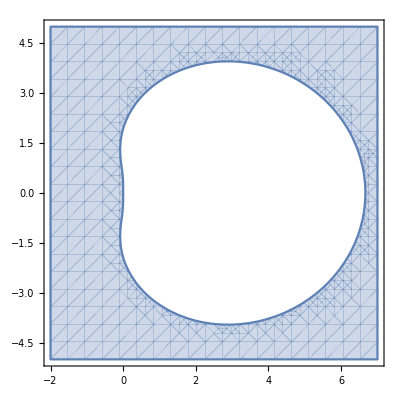

```mathematica
RegionPlot[root[x+I y]≤1,{x,-2,7},{y,-5,5}]
```

## Problem 3

```mathematica
k1= y l;
k2 =Expand[y l(1+1/2 l)];
k3=Expand[y l(1+1/2 l(1+1/2 l))];
k4=Expand[y l(1+l(1+1/2 l(1+1/2 l)))];
```

```mathematica
factor=Simplify[y+1/6(k1+2k2+2k3+k4)]/y;
```

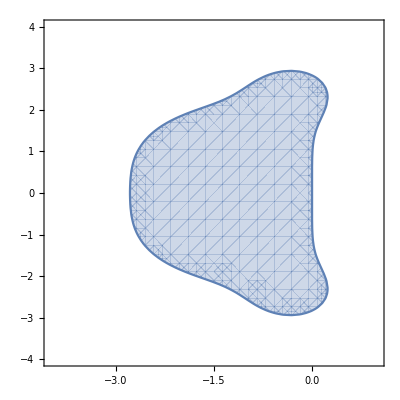

```mathematica
R[w_]=factor/.{l->w};
RegionPlot[Abs[R[x+I y]]≤1,{x,-4,1},{y,-4,4}]
```

```mathematica
(*Where does this region intersect the real axis?*)
N[Solve[R[w]==1,w][[1]]]
N[Solve[R[w]==1,w][[4]]]
```

{w→0.}

{w→-2.78529}

```mathematica
(*Where does this region intersect the imaginary axis?*)
Expand[R[w I] *R[-w I]]
Solve[Expand[R[w I] *R[-w I]]==1,w]
```

1-w^6/72+w^8/576

{{w→0},{w→0},{w→0},{w→0},{w→0},{w→0},{w→-2 √2},{w→2 √2}}

## Problem 5

```mathematica
Solve[{a0 m a + a0 c - a1 m == g1,b0 m a + b0c - b1 m ==g2},{m,c}]
```

{{m→-(b0c-g2)/(a b0-b1),c→-(-a a0 b0c+a1 b0c-a b0 g1+b1 g1+a a0 g2-a1 g2)/(a0 (a b0-b1))}}